```mathematica
S[x_]:=Exp[-Abs[x]/2]
Subscript[k, w][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, w]])Exp[Sqrt[Subscript[β, w]](x-ξ)],x<ξ}}]
Subscript[k, l][x_,ξ_]:=Piecewise[{{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](ξ-x)],x>ξ},{1/(2Sqrt[Subscript[β, l]])Exp[Sqrt[Subscript[β, l]](x-ξ)],x<ξ}}]
var=Rationalize[{Subscript[α, w]->50.58,Subscript[β, w]->3.85/0.38,Subscript[η, w]->1/(0.38*10)*Q,Subscript[α, l]->192.2/(1.89*10),Subscript[β, l]->3.85/1.89,Subscript[η, l]->1/(1.89*10)*Q,Subscript[a, 0]->0.6,Subscript[a, 1]->0.38,M->0.38/1.89,Subscript[L, 0]->-1+ϵ,Subscript[L, 1]->1+ϵ}];
```

```mathematica
Subscript[T, 0][ξ_]:=Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ<Subscript[A, 0]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]<Subscript[L, 0]/.var]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,-∞,Subscript[A, 0]},Assumptions->ξ<Subscript[A, 0]<Subscript[L, 0]/.var]
Subscript[F, 0][ξ_]=Refine[Expand[Subscript[T, 0][ξ]/.var],{0<ϵ<1,ξ<Subscript[A, 0]<Subscript[L, 0]}/.var];
```

```mathematica
Subscript[T, 1][ξ_]:=Limit[Subscript[c, 2] Subscript[k, w][x,ξ]-Subscript[c, 1] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ<Subscript[L, 0]]-Limit[Subscript[c, 0] Subscript[k, w][x,ξ]+ D[Subscript[k, w][x,ξ], x],x->Subscript[A, 0],Assumptions->ξ>Subscript[A, 0]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0]/.var,Subscript[A, 0]<Subscript[L, 0]/.var}]+Subscript[η, w](1-Subscript[a, 1])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[A, 0],Subscript[L, 0]}/.var,Assumptions->{Subscript[A, 0]<ξ<Subscript[L, 0]/.var,Subscript[A, 0]<Subscript[L, 0]/.var}]
Subscript[F, 1][ξ_]=Refine[Expand[Subscript[T, 1][ξ]/.var],{0<ϵ<1,Subscript[A, 0]<ξ<Subscript[L, 0]}/.var];
```

```mathematica
Subscript[T, 2][ξ_]:=Limit[M Subscript[c, 4] Subscript[k, l][x,ξ]-Subscript[c, 3] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ<Subscript[L, 1]]-Limit[M Subscript[c, 2] Subscript[k, l][x,ξ]-Subscript[c, 1] D[Subscript[k, l][x,ξ], x],x->Subscript[L, 0],Assumptions->ξ>Subscript[L, 0]]-Subscript[α, l] Integrate[Subscript[k, l][x,ξ],{x,Subscript[L, 0],Subscript[L, 1]}/.var,Assumptions->0<ϵ<1]+Subscript[η, l](1-Subscript[a, 0])Integrate[Subscript[k, l][x,ξ]S[x],{x,Subscript[L, 0],Subscript[L, 1]}/.var,Assumptions->0<ϵ<1]
Subscript[F, 2][ξ_]=Refine[PiecewiseExpand[Subscript[T, 2][ξ]/.var],{0<ϵ<1,Subscript[L, 0]<ξ<Subscript[L, 1]/.var}];
```

```mathematica
Subscript[T, 3][ξ_]:=-Limit[Subscript[c, 4] Subscript[k, w][x,ξ]-Subscript[c, 3] D[Subscript[k, w][x,ξ], x],x->Subscript[L, 1],Assumptions->ξ>Subscript[L, 1]]-Subscript[α, w] Integrate[Subscript[k, w][x,ξ],{x,Subscript[L, 1],∞}/.var,Assumptions->{Subscript[L, 1]<ξ}/.var]+Subscript[η, w](1-Subscript[a, 0])Integrate[Subscript[k, w][x,ξ]S[x],{x,Subscript[L, 1],∞}/.var,Assumptions->{Subscript[L, 1]<ξ}/.var]
Subscript[F, 3][ξ_]=Refine[Expand[Subscript[T, 3][ξ]/.var],{0<ϵ<1,Subscript[L, 1]<ξ}/.var];
```

```mathematica
Subscript[eqn, 0]=Subscript[F, 0][Subscript[A, 0]]+1==0;
Subscript[eqn, 1]=Subscript[F, 1][Subscript[A, 0]]+1==0;
Subscript[eqn, 2]=Subscript[F, 2][Subscript[L, 0]]- Subscript[F, 1][Subscript[L, 0]]==0/.var;
Subscript[eqn, 3]=Subscript[F, 2][Subscript[L, 1]]- Subscript[F, 3][Subscript[L, 1]]==0/.var;
Subscript[eqn, 4]=Subscript[F, 2]'[Subscript[L, 0]]-M Subscript[F, 1]'[Subscript[L, 0]]==0/.var;
Subscript[eqn, 5]=Subscript[F, 2]'[Subscript[L, 1]]-M Subscript[F, 3]'[Subscript[L, 1]]==0/.var;
```

```mathematica
Beep[]
```

```mathematica
(*Finding what Q's has solution on this form*)
Subscript[Q, min]=540;
Subscript[Q, max]=590;
n=2(Subscript[Q, max]-Subscript[Q, min])+1;
Subscript[ϵ, test]=0.001;
sols={};
Monitor[
For[i=0,i<n,i++,
tempQ={Q->Rationalize[Subscript[Q, min]+(Subscript[Q, max]-Subscript[Q, min])*i/(n-1),0],ϵ->Rationalize[Subscript[ϵ, test],0]};
sol=Quiet[FindRoot[{Subscript[eqn, 0],Subscript[eqn, 1],Subscript[eqn, 2],Subscript[eqn, 3],Subscript[eqn, 4],Subscript[eqn, 5]}/.tempQ,{{Subscript[c, 0],0},{Subscript[c, 1],0},{Subscript[c, 2],0},{Subscript[c, 3],0},{Subscript[c, 4],0},{Subscript[A, 0],-1.5}}/.tempQ,MaxIterations->100,WorkingPrecision->30]];
sol=Join[sol,tempQ,var/.tempQ];
Quiet[conds=Subscript[A, 0]<Subscript[L, 0]&&
NMaxValue[{Subscript[F, 0][x],-10<x<Subscript[A, 0]}/.sol,x]<-0.99999&&
NMinValue[{Subscript[F, 1][x],Subscript[A, 0]<x<Subscript[L, 0]}/.sol,x]>-1.00001&&
NMaxValue[{Subscript[F, 2][x],Subscript[L, 0]<x<Subscript[L, 1]}/.sol,x]<0.00001&&
NMaxValue[{Subscript[F, 3][x],Subscript[L, 1]<x<10}/.sol,x]<-0.99999/.sol];
If[conds,M[x_]=Rationalize[Piecewise[{{Subscript[F, 0][x],x<Subscript[A, 0]},{Subscript[F, 1][x],Subscript[A, 0]<=x<Subscript[L, 0]},{Subscript[F, 2][x],Subscript[L, 0]<=x<=Subscript[L, 1]},{Subscript[F, 3][x],Subscript[L, 1]<x}}/.sol],0];
NUM=12001;
points=SetPrecision[Table[-6+12(i-1)/(NUM-1),{i,NUM}],20];
nSolution=N[Map[M, points]];
sols=Join[sols,{{N[Q/.sol],N[M[0]/.sol],N[M[ϵ]/.sol],nSolution}}],Nothing];
],{N[i/n],N[Q/.tempQ]}]
Beep[]
```

```mathematica
Export["C:\\masterA GitHub\\Code\\Exponential\\Continent Offset 0.001\\2 - IceWaterSnowIce.csv",sols,Format->Table];
```

556

{c_0→2.840037768309442353552540841189636900224319338805839127344289833400586678922374891126971921984345581,c_1→-0.9915862263753975214603910955737375860122164482620377009764707999606364752671838771979406813177535294,c_2→2.79259154331960418736976420594039528895337507844460515760896288215073302356639844991818951289449096,c_3→-1.120547776989771171331188641209135586123085979383359605304309127460386147127675058661348250585545553,c_4→-2.923547103199903596530762710657272629883736277846925768980269050255461122206061249757420287342561558,A_0→-0.9529875122011311315665363428420014554206048921262397944795586670395639015284135297988060925077508599}

True True True

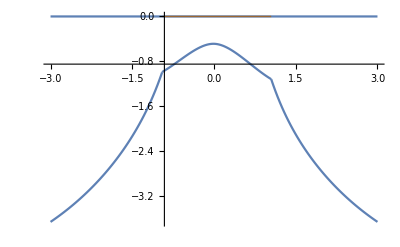

```mathematica
Subscript[Q, temp]=556
tempQ={Q->Rationalize[Subscript[Q, temp],0],ϵ->Rationalize[0.05,0]};
sol=FindRoot[{Subscript[eqn, 0]/.tempQ,Subscript[eqn, 1]/.tempQ,Subscript[eqn, 2]/.tempQ,Subscript[eqn, 3]/.tempQ,Subscript[eqn, 4]/.tempQ,Subscript[eqn, 5]/.tempQ},{{Subscript[c, 0],Round[Subscript[c, 0]/.sol,0.001]},{Subscript[c, 1],Round[Subscript[c, 1]/.sol,0.001]},{Subscript[c, 2],Round[Subscript[c, 2]/.sol,0.001]},{Subscript[c, 3],Round[Subscript[c, 3]/.sol,0.001]},{Subscript[c, 4],Round[Subscript[c, 4]/.sol,0.001]},{Subscript[A, 0],-1.5}},MaxIterations->1000,WorkingPrecision->100]
sol=Rationalize[Join[sol,tempQ],0];
sol=Join[sol,var/.sol];
Subscript[p, 0]=Plot[Subscript[F, 0][x]/.sol,{x,-3,Subscript[A, 0]/.sol},PlotRange->All,WorkingPrecision->30];
Subscript[p, 1]=Plot[Subscript[F, 1][x]/.sol,{x,Subscript[A, 0]/.sol,Subscript[L, 0]/.sol},PlotRange->All,WorkingPrecision->30];
Subscript[p, 2]=Plot[Subscript[F, 2][x]/.sol,{x,Subscript[L, 0]/.sol,Subscript[L, 1]/.sol},PlotRange->All,WorkingPrecision->30];
Subscript[p, 3]=Plot[Subscript[F, 3][x]/.sol,{x,Subscript[L, 1]/.sol,3},PlotRange->All,WorkingPrecision->30];
Subscript[p, 4]=Plot[0,{x,-3,3},PlotRange->All];
Subscript[p, 5]=Plot[0,{x,Subscript[L, 0],Subscript[L, 1]}/.sol,PlotRange->All,PlotStyle->{Brown,Thick}];
Print[Subscript[A, 0]<Subscript[L, 0]/.sol," ",NMaxValue[{Subscript[F, 2][x],Subscript[L, 0]<x<Subscript[L, 1]}/.sol,x]<0," ",N[Subscript[F, 2][Subscript[L, 1]]/.sol]<-1]
Show[Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5],PlotRange->All]
```